Q1: Find the first three roots of the Bessel function

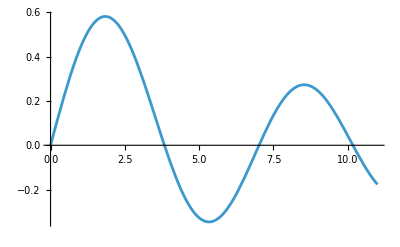

```mathematica
Plot[BesselJ[1,x],{x,0,11},PlotRange->All]
```

```mathematica
x1/.FindRoot[BesselJ[1,x1]==0,{x1,3}]
```

3.83171

```mathematica
x2/.FindRoot[BesselJ[1,x2]==0,{x2,7}]
```

7.01559

```mathematica
x3/.FindRoot[BesselJ[1,x3]==0,{x3,10}]
```

10.1735

```mathematica
Plot[BesselJ[1,x],{x,0,11},PlotRange->All]
```

-Graphics-

---------------------------
Q4: Solve the following initial-value problem using both DSolve and NDSolve. Compare your answers by plotting them.
y’’(x) - x y(x) = 0
y(0) = 1
y’(0) = - 3^(1/3)Gamma(2/3)/Gamma(1/3)

```mathematica
solDS=DSolve[{y''[x]-x y[x]==0,y[0]==1, y'[0]==-3^(1/3)Gamma[2/3]/Gamma[1/3]},y[x],x]
```

{{y[x]→3^(2/3) AiryAi[x] Gamma[2/3]}}

```mathematica
solND=NDSolve[{y''[x]-x y[x]==0,y[0]==1,y'[0]==-3^(1/3)Gamma[2/3]/Gamma[1/3]},y[x],{x,0,20}, AccuracyGoal->10,PrecisionGoal->10,MaxSteps->Infinity]
```

{{y[x]→InterpolatingFunction[…][x]}}

```mathematica
Plot[{y[x]/. solDS[[1]],y[x]/. solND[[1]]},{x,0,20},PlotRange->All,PlotLegends->{"DSolve","NDSolve"}]
```